```mathematica
T[p_] := (p(p+1))/2
```

```mathematica
R[p_] := Sum[(p!)/((p-j)!),{j,1,p}]
```

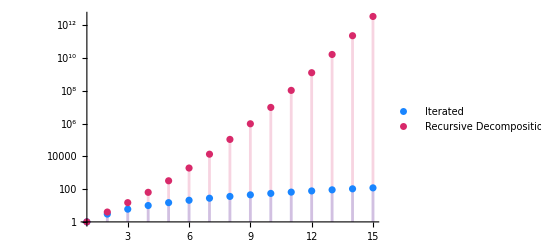

```mathematica
plot = DiscretePlot[{T[p],R[p]},{p,1,15},PlotLegends->{Style["Iterated",FontFamily->"Century"],Style["Recursive\nDecompositions",FontFamily->"Century"]},PlotStyle->{RGBColor[25/255,133/255,255/255],RGBColor[216/255,41/255,106/255]},ScalingFunctions->{None,"Log"},Ticks->{Automatic,Table[{10^n,Superscript[10,n]},{n,0,10,2}]},AxesLabel->{p}]
```

```mathematica
Export["plot.svg",plot]
```

plot.svg